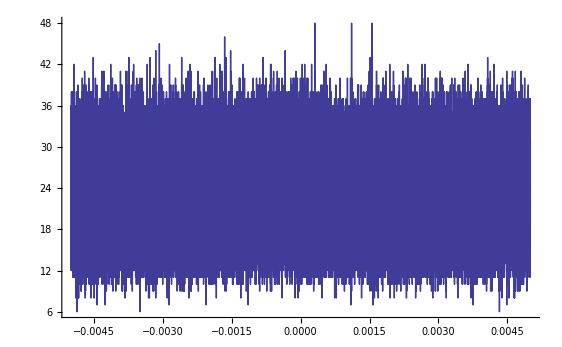

```mathematica
file = "D:\\Users\\Chronos\\Documents\\GitHub\\PT2_time_autocorr\\out.out";

raw = Import[file];
data = raw[[5;;All]];

ListLinePlot[data,PlotRange->All,AxesOrigin->{0,0}]
```

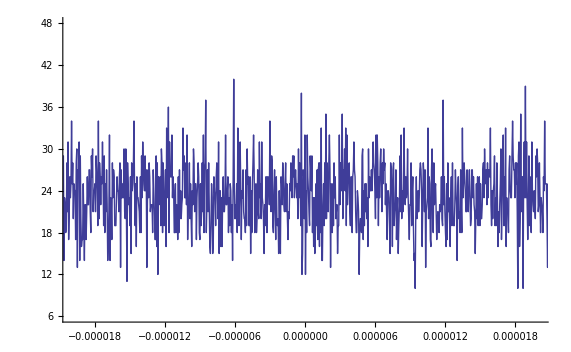

```mathematica
edge = 0.00002;

ListLinePlot[data
,PlotRange->{{-edge,edge},All}
,AxesOrigin->{0,0}
]
```